```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, R, t, Hfunc, Zfunc, Rfunc, fixedPoints, 
   phasePlot, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* Define the differential equations *)
  eqns = {
    H'[t] == - H[t] Z[t]+αH,
    Z'[t] == H[t] Z[t] - δZ H[t] Z[t],
    R'[t] == δZ H[t] Z[t]
  };
  
  jMatrix = {
   {-Z, - H, 0},
   {(1 - δZ) Z, (1 - δZ) H, 0},
   {δZ Z, δZ H, 0}
	};
  parameterSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-10,10},{-10,10}}];
  (* Solve the equations numerically *)
  sol = NDSolve[
    {eqns, 
     H[0] == H0/H0, 
     Z[0] == Z0/H0, 
     R[0] == R0/H0
    }, 
    {H, Z, R}, 
    {t, 0, tmax}
  ];
  
  (* Extract solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  finalTraceJ = traceJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), δZ -> δZ };
  finalDetJ = detJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), δZ -> δZ };
  
  (* Generate phase space stream plot *)
  phasePlot = 
   StreamPlot[
    Evaluate[{
      - H Z+αH, 
      H Z - δZ H Z
    } /. {R -> Rfunc[tmax]}],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
  
  (* Display the results *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (S)", "Zombies (Z)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Purple, Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlot,
    Show[
		parameterSpace,
		ListPlot[{{finalDetJ,finalTraceJ}},PlotStyle->PointSize[Medium]]
	]
   }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{αH, 0.01, "Addition of humans (alpha_H)"}, 0, 5, 0.001},
 {{δZ, 1.1, "Dimensionless zombie removal rate (delta_Z)"}, 0, 2, 0.01},
 {{H0, 500, "Initial humans (S0)"}, 0, 5000, 1},
 {{Z0, 100, "Initial zombies (Z0)"}, 0, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 100, "Simulation time"}, 10, 1000000, 1}
]
```

## Eigen Analysis

```mathematica
jMatrix = {
   {-Z, - H, 0},
   {(1 - δZ) Z, (1 - δZ) H, 0},
   {δZ Z, δZ H, 0}
	};
	
fixedPoint1 = {Z -> 0};
fixedPoint2 = {H -> 0};
fixedPoint3 = {H -> 0, Z -> 0};

genEigenVals = Eigenvalues[jMatrix]
eigenVals1 = Eigenvalues[jMatrix /. fixedPoint1]
eigenVals2 = Eigenvalues[jMatrix /. fixedPoint2]
eigenVals3 = Eigenvalues[jMatrix /. fixedPoint3]
```

{0,0,H-Z-H δZ}

{0,0,H (1-δZ)}

{-Z,0,0}

{0,0,0}

## Bifurcation Analysis

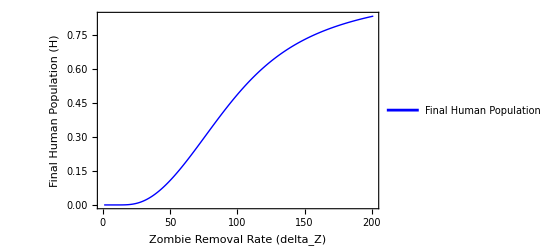

```mathematica
finalHValues = Table[
  Module[
    {sol, Hfunc, finalH},
    (* Define the differential equations *)
    eqns = {
      H'[t] == - H[t] Z[t],
      Z'[t] == H[t] Z[t] - δZ H[t] Z[t],
      R'[t] == δZ  H[t] Z[t]
    };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 500/500, 
       Z[0] == 100/500,
       R[0] == 0/500
      },
      {H, Z, R}, 
      {t, 0, 1000000}
    ];
    
    (* Extract the function for H *)
    Hfunc = H /. sol[[1]];
    
    (* Extract the final value of H at time tmax *)
    finalH = Hfunc[1000000];
    
    (* Return the final human value for plotting *)
    finalH
  ],
  {δZ, 0, 2, 0.01} (* Vary deltaZ from 0 to 1 in steps of 0.01 *)
];

(* Plot final human population as a function of deltaZ *)
ListLinePlot[finalHValues, 
 PlotRange -> All,
 PlotLegends -> {"Final Human Population (H) vs. deltaZ"}, 
 PlotStyle -> {Blue, Thick},
 AxesLabel -> {"Zombie Removal Rate (delta_Z)", "Final Human Population (H)"},
 Frame -> True,
 FrameLabel -> {"Zombie Removal Rate (delta_Z)", "Final Human Population (H)"}
]
```

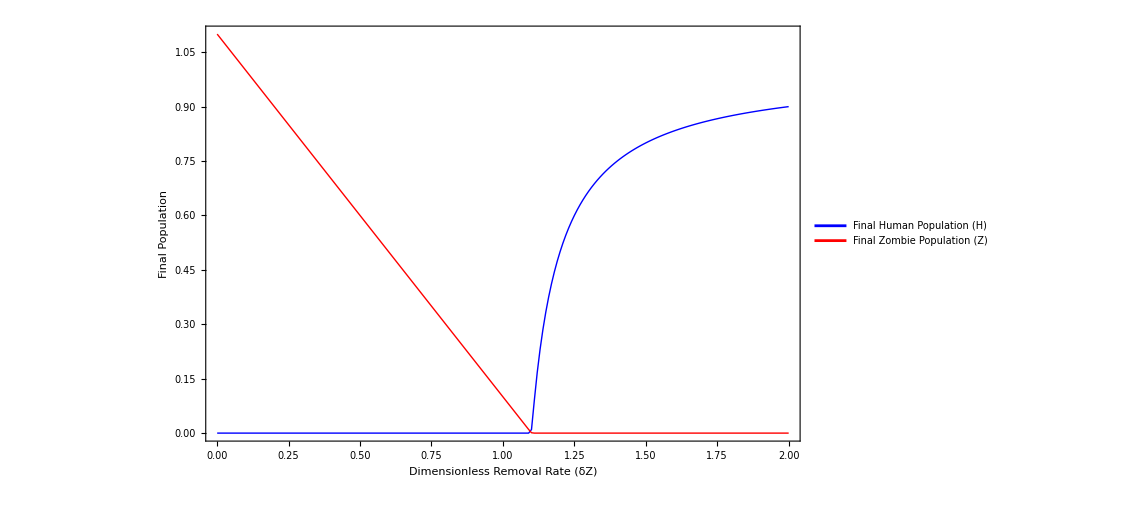

```mathematica
(* Compute final values of H and Z for varying deltaZ *)
finalValues = Table[
  Module[
    {sol, Hfunc, Zfunc, finalH, finalZ},
    (* Define the differential equations *)
    eqns = {
      H'[t] == - H[t] Z[t],
      Z'[t] == H[t] Z[t] - δZ H[t]Z[t],
      R'[t] == δZ H[t]Z[t]
    };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 1000/1000, 
       Z[0] == 100/1000,
       R[0] == 0/500
      },
      {H, Z, R}, 
      {t, 0, 1000}
    ];
    
    (* Extract the functions for H and Z *)
    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    
    (* Extract the final values of H and Z at time tmax *)
    finalH = Hfunc[1000];
    finalZ = Zfunc[1000];
    
    (* Return the deltaZ and final values for plotting *)
    {δZ, finalH, finalZ}
  ],
  {δZ, 0, 2, 0.01} (* Vary deltaZ from 0 to 2 in steps of 0.01 *)
];

(* Separate deltaZ, H, and Z values for plotting *)
deltaZValues = finalValues[[All, 1]];
finalHValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];

(* Plot final human and zombie populations as a function of deltaZ *)
ListLinePlot[
  {
   Transpose[{deltaZValues, finalHValues}],
   Transpose[{deltaZValues, finalZValues}]
  },
  PlotRange -> All,
  PlotLegends -> {"Final Human Population (H)", "Final Zombie Population (Z)"},
  PlotStyle -> {{Blue, Thick}, {Red, Thick}},
  AxesLabel -> {"Zombie Removal Rate (δZ)", "Final Population"},
  Frame -> True,
  FrameLabel -> {"Dimensionless Removal Rate (δZ)", "Final Population"}
]
```

```mathematica
(* Solve the steady-state equations for fixed points *)
fixedPoints = Solve[
  {
    -H*Z == 0,
    H*Z - deltaZ*H*Z == 0,
    deltaZ*H*Z == 0
  },
  {H, Z}
];

Print["Fixed Points:", fixedPoints];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Fixed Points:{{H→0},{Z→0}}